```mathematica
Clear["Global`*"]
```

```mathematica
mfile="E:\\Users\\byrdie\\School\\Classes\\EELE582_OpticalDesign\\FinalProject\\meta.bin";
dfile = "E:\\Users\\byrdie\\School\\Classes\\EELE582_OpticalDesign\\FinalProject\\psf.bin"
```

E:\Users\byrdie\School\Classes\EELE582_OpticalDesign\FinalProject\psf.bin

```mathematica
f = BinaryRead[mfile,"Real64" ]
nx = BinaryRead[mfile,"Integer32" ]
ny = BinaryRead[mfile,"Integer32" ]
minX = BinaryRead[mfile,"Real64" ] 
minY = BinaryRead[mfile,"Real64" ]
dx = BinaryRead[mfile,"Real64" ]
dy = BinaryRead[mfile,"Real64" ]
```

500.

256

256

-0.109375

-0.109375

0.000854492

0.000854492

```mathematica
Close[mfile]
```

E:\Users\byrdie\School\Classes\EELE582_OpticalDesign\FinalProject\meta.bin

```mathematica
data =BinaryReadList[dfile,"Real64"];
```

```mathematica
psf =ArrayReshape[data,{nx,ny}];
```

```mathematica
ListDensityPlot[psf,PlotRange->Full,ColorFunction->"Rainbow"]
```

-Graphics-

#### Rescale the point spread function

0.6 "

0.352503 "

1.70211

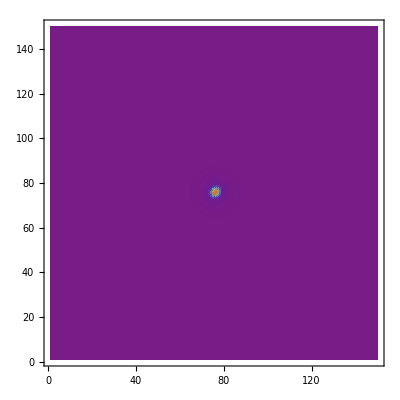

```mathematica
aiaPix = 0.6 Quantity[, "ArcSeconds"]
psfPix = UnitConvert[2/nx ArcTan[-minX/f]Quantity[, "Radians"],"ArcSeconds"]
ratio =aiaPix/psfPix
ipsf = ListInterpolation[psf];
aiaPsf = Table[ipsf[x,y],{x,1,nx,ratio},{y,1,ny,ratio}];
ListDensityPlot[aiaPsf,PlotRange->Full,ColorFunction->"Rainbow"]
```

```mathematica
sun =ImageCrop[Import["E:\\Users\\byrdie\\School\\Classes\\EELE582_OpticalDesign\\FinalProject\\image_sim\\2017_04_23__02_01_41_13__SDO_AIA_AIA_304.jp2"],{512,512}] //ImageAdjust
```

-Graphics-

```mathematica
ImageConvolve[sun,aiaPsf] //ImageAdjust
```

-Graphics-

```mathematica
1.74356222762481-1.74791571142519
```

-0.00435348